## Install functions

Execute the following cell to install some useful functions (place cursor on next line and press shift enter):

```mathematica
minVersion=9;

updateInitFile::tooLowVersionError="You need at least Mathematica version "<>ToString@minVersion<>" to use this init file.";
updateInitFile::networkError="Failed to retrieve the latest init.m version from github.";

If[minVersion>$VersionNumber,
Message[updateInitFile::tooLowVersionError],
initPath = ToFileName[{$UserBaseDirectory, "Kernel"}, "init.m"];
newest = URLFetch@"https://raw.github.com/Tyilo/Mathematica-init.m/master/init.m";
If[newest===$Failed||StringSplit[newest,"\n"][[1]]!="(* ::Package:: *)",
Message[updateInitFile::networkError],
WriteString[f = OpenWrite@initPath, newest];
Close@f;
MessageDialog["Mathematica's init.m has been updated!
Restart Mathematica to apply the changes."];
];
];
```

## Shortcuts

Shortcut | Result
Ctrl 2  | (√□)
Ctrl 2,Ctrl 5 | (□^(1/□))
Ctrl 6 | (□^□)
Ctrl - | (□_□)
Ctrl -,Ctrl 5 | (□_□^□)
Ctrl / | (□/□)
Ctrl ⌤ | (□
□)
Ctrl , | (□ | □)
⇧ ⌤ | [Evaluate]
⌘ ⌤ | [Evaluate in place]
□ | □
□ | □
□ | □
□ | □

## Macros

Macro | Result
EscAEsc | Α
EscBEsc | Β
EscDEsc | Δ
... | ...
EscaEsc | α
EscbEsc | β
EscdEsc | δ
... | ...
EscinfEsc | ∞
EscdegEsc | °
Esc+-Esc | ±
Esc!=Esc | ≠
Esc>=Esc | ≥
Esc<=Esc | ≤
Esc.Esc | ·
Esc&&Esc
EscandEsc | ∧
Esc||Esc
EscorEsc | ∨
EscelemEsc | ∈
EscesEsc | ∅
Esc->Esc | →
EscdsREsc | ℝ
EscpdEsc | ∂
□ | □
EscintEsc | ∫
EscinttEsc | ∫□ⅆ□
EscdinttEsc | ∫_□^□ □ⅆ□
□ | □
EscpwEsc | {
Escl|EscxEscr|Esc | |x|
Escl||EscxEscr||Esc | ‖x‖
EsclfEscxEscrfEsc | ⌊x⌋
EsclcEscxEscrcEsc | ⌈x⌉

## Basic functionality

### Calling a function

There a several methods for calling a function.
All of these expressions are equivalent:

```mathematica
Sin[2]
```

sin(2)

```mathematica
Sin@2
```

sin(2)

```mathematica
2//Sin
```

sin(2)

If the function takes more than 1 argument only [ ] can be used:

```mathematica
Max[100,2]
```

100

### Mapping a function to a list of values

If you have a list of values like so:

```mathematica
list={1,5,6,10,2};
```

You can apply a function to all the values in the list, by using Map or /@:

```mathematica
Map[Sin,list]
```

{sin(1),sin(5),sin(6),sin(10),sin(2)}

```mathematica
Sin/@list
```

{sin(1),sin(5),sin(6),sin(10),sin(2)}

### Approximating a value

As Mathematica calculates values symbolically with infinite precision, expressions like Sin[2] will return Sin[2].
To approximate the value, you can use the function N:

```mathematica
Sin[2]//N
```

0.909297

You can also specify the number of significant digits you want:

```mathematica
N[Sin[2],2]
```

0.91

```mathematica
N[Sin[2],30]
```

0.909297426825681695396019865912

### Differentiating an expression

To differentiate a function you can use one of the following functions:

```mathematica
D[x^2+5x,x]
```

2 x+5

∂ can be entered via EscpdEsc:

```mathematica
D[(x^2+5x), x]
```

2 x+5

### Integrating an expression

To integrate an expression you can use the Integrate function:

```mathematica
Integrate[2x+5,x]
```

x^2+5 x

This template can be entered with EscinttEsc:

```mathematica
∫(2x+5)ⅆx
```

x^2+5 x

To get a definite integral, you can use Integrate or EscdinttEsc:

```mathematica
Integrate[2x+5,{x,0,5}]
```

50

```mathematica
∫_0^5 (2x+5)ⅆx
```

50

### Plotting an expression

You can plot an expression like so:

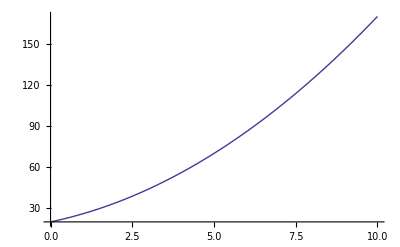

```mathematica
Plot[x^2+5x+20,{x,0,10}]
```

0 and 10 is the interval on the x-axis.

As you can see the axes doesn’t cross at 0, 0.
To fix this, use the option AxesOrigin:

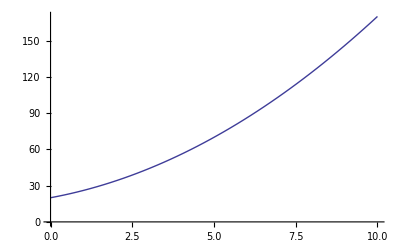

```mathematica
Plot[x^2+5x+20,{x,0,10},AxesOrigin->{0,0}]
```

You can also add labels to the axes like so:

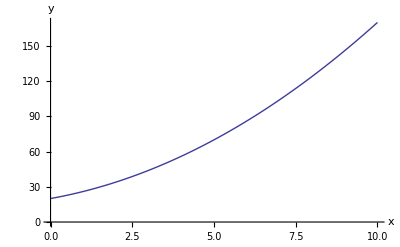

```mathematica
Plot[x^2+5x+20,{x,0,10},AxesOrigin->{0,0},AxesLabel->{"x","y"}]
```

Changing the first argument of Plot to a list allows us to plot multiple expression on one plot:

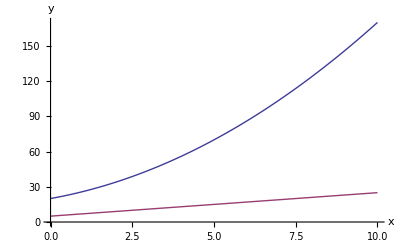

```mathematica
Plot[{x^2+5x+20,2x+5},{x,0,10},AxesOrigin->{0,0},AxesLabel->{"x","y"}]
```

You can also add a legend to the plot to show which function is which:

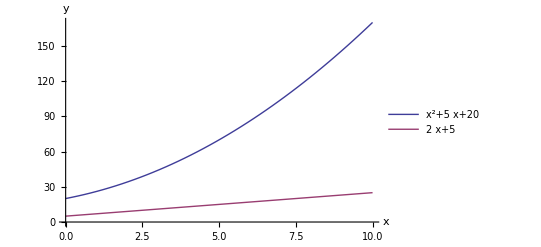

```mathematica
Plot[{x^2+5x+20,2x+5},{x,0,10},AxesOrigin->{0,0},AxesLabel->{"x","y"},PlotLegends->"Expressions"]
```

## Builtin functions

### FindFit

Generate a table of data following a formula:

```mathematica
formula=a·x^2+b·x+c;
formula1=formula/.{a->10,b->-6,c->5}
data=Table[{x,formula1},{x,-3,3}]
```

10 x^2-6 x+5

(-3 | 113
-2 | 57
-1 | 21
0 | 5
1 | 9
2 | 33
3 | 77)

Try to fit the data to the formula:

```mathematica
params=FindFit[data,formula,{a,b,c},x]
formula/.params
```

{a→10.,b→-6.,c→5.}

10. x^2-6. x+5.

### NonlinearModelFit

```mathematica
fit=NonlinearModelFit[({{1, 100}, {5, 1150}, {7, 2600}, {10, 4400}, {14, 7500}}),a x^2+b x+c,{a,b,c},x]
Normal[fit]
fit["RSquared"]
```

FittedModel[25.3551 x^2+198.445 x-199.843]

25.3551 x^2+198.445 x-199.843

0.998577

## Functions in my init.m made by me

### updateInitFile

Updates the init file by downloading the newest version from GitHub. Required internet access.

```mathematica
updateInitFile[]
```

### reloadInitFile

Reloads the init file without needing to restart Mathematica. May not always work.

```mathematica
reloadInitFile[]
```

### fixMathematica

Resets the users settings, which sometimes can cause problems.
You should restart Mathematica after running the function.

```mathematica
fixMathematica[]
```

### SinDeg, CosDeg, TanDeg

Like the builtin functions Sin, Cos & Tan but takes a number in degrees as input instead of radians.

### ArcSinDeg, ArcCosDeg, ArcTanDeg

Like the builtin functions ArcSin, ArcCos & ArcTan but returns a number in degrees instead of radians.

### allProperties

Shows all properties for an element in ElementData, ChemicalData, AstronomicalData, etc.

```mathematica
OpenerView[{"Show output",allProperties[ChemicalData,"Water"]}]
```

### intInterval

Calculates the definite integral from an indefinite integral:

```mathematica
f=x^2;
F=∫fⅆx
```

x^3/3

```mathematica
intInterval[F,{x,1,10}]
```

333

As you can see we get the same result as calculating the definite integral directly:

```mathematica
∫_1^10 fⅆx
```

333

### plotIntersect

Plots two functions and adds a point where they intersect.

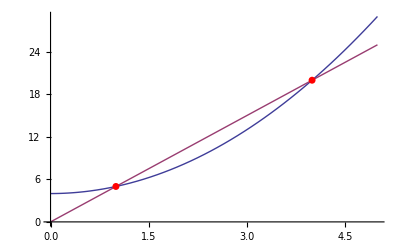

```mathematica
plotIntersect[x^2+4,5x,{x,0,5}]
```

### plotDefiniteIntegral

Plot a definite integral by coloring the area covered:

```mathematica
∫_0^(3/2 π) Sin[x]ⅆx
```

1

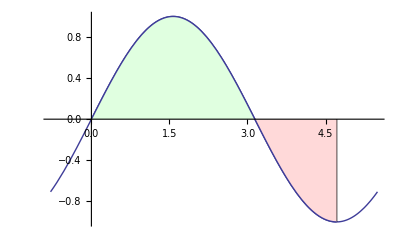

```mathematica
plotDefiniteIntegral[Sin[x],{x,0,3/2 π}]
```

A third argument can be used to specify the margin:

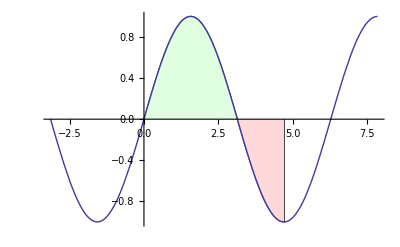

```mathematica
plotDefiniteIntegral[Sin[x],{x,0,3/2 π},π]
```

### fitPlot

Takes the same arguments as NonlinearModelFit, but outputs a plot of the points with a fitted line instead:

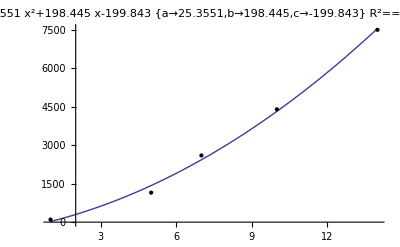

```mathematica
fitPlot[({{1, 100}, {5, 1150}, {7, 2600}, {10, 4400}, {14, 7500}}),a x^2+b x+c,{a,b,c},x]
```

### plotWithPoints

Like normal Plot, but takes a list of x-values as third argument and adds a point to the plot for every x-value:

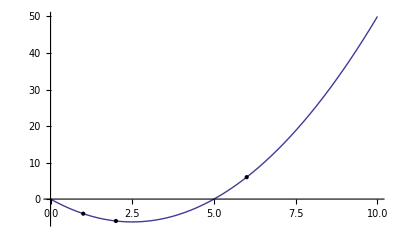

```mathematica
plotWithPoints[x^2-5x,{x,0,10},{1,2,6}]
```

### plot3DCrossSection

```mathematica
plot3DCrossSection[x^2-y^2,{x,-3,3},{y,-3,3}]
```

### lineElementPlot

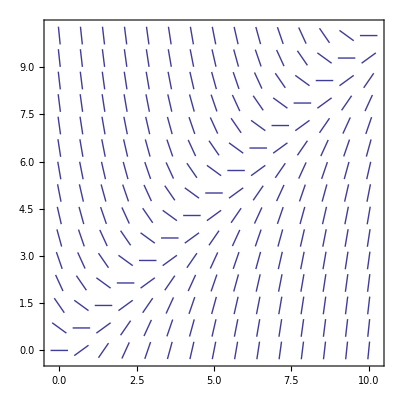

```mathematica
lineElementPlot[x-y,{x,0,10},{y,0,10}]
```

### removeSubscript

Removes subscripts from a string:

```mathematica
removeSubscript["H_2O"]
```

H2O

### molecularWeight

Calculates the molecular weight of a compound based on its molecular formula:

```mathematica
molecularWeight["CH_3COOH"]
```

60.052

### chemicalTable

List all chemicals matching a name/formula:

```mathematica
chemicalTable["C2H4O2"]
```

### deltaH, deltaS, deltaG

Calculates ΔH^⊖, ΔS^⊖ and ΔG^⊖ for a chemical reaction:

```mathematica
deltaH[2"NO(g)"+"O_2(g)"->2"NO_2(g)"]
```

-116.2

```mathematica
#["CH_3CH_2OH(l)"->"C_2H_4(g)"+"H_2O(l)"]&/@{deltaH,deltaS,deltaG}
```

{44.07,128.55,5.94}

### firstDropWhile

Returns the first element in a list that doesn’t satisfy a condition:

```mathematica
firstDropWhile[{1,4,2,7,3},#<5&]
```

7

It returns Null if every element satisfies the condition:

```mathematica
firstDropWhile[{1,4,2},#<5&]
```

### stringCapitalize

Capitalizes a string:

```mathematica
stringCapitalize["hello world"]
```

Hello world

### unitFullName

Returns the full name of an unit from its abbreviation, which can then be used in Quantity, UnitConvert, etc.

```mathematica
unitFullName["km"]
```

Kilometers

```mathematica
Quantity[10,Evaluate@unitFullName["km"]]
UnitConvert[%,Evaluate@unitFullName["m"]]
```

10

10000

### constantFullName

Like unitFullName but for constants:

```mathematica
constantFullName["G"]
```

GravitationalConstant

```mathematica
constantFullName["R"]
```

MolarGasConstant

### solvePolynomialCoordinates

Given a table with n coordinates, finds the (n-1)th degree polynomial that passes through all the points:

```mathematica
solvePolynomialCoordinates[({{10, 4}, {3, 6}, {5, 11}})]
```

{a→-39/70,b→487/70,c→-69/7}

```mathematica
a·x^2+b·x+c/.%
```

-(39 x^2)/70+(487 x)/70-69/7

### walkInt

Shows the steps needed to integrate an expression:

```mathematica
walkInt[2^(x^2+5)·7x,x]
```

∫7 2^(5+x^2) xⅆx

=  7 ∫2^(5+x^2) xⅆx

=  (7 2^(5+x^2) x)/((ⅆ/ⅆx(5+x^2)) log(2))

=  (7 2^(5+x^2) x)/((ⅆ/ⅆx 5+ⅆ/ⅆx x^2) log(2))

=  (7 2^(5+x^2) x)/((ⅆ/ⅆx x^2) log(2))

=  (7 2^(4+x^2))/(log(2))

(7 2^(x^2+4))/(log(2))

## Functions in my init.m made by others

### manToGif

Creates an animated gif from a Manipulate object. The third argument is the speed of the gif.

```mathematica
man=Manipulate[Plot[a x^2,{x,-10,10},PlotRange->{All,{-400,400}}],{a,-4,4}]
```

```mathematica
manToGif[man,"test",1];
"GIF was saved to: "<>AbsoluteFileName[%]
```

GIF was saved to: /Users/Tyilo/test.gif

### numPlot

Draws lines or arrows on a number line:

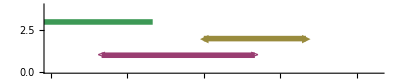

```mathematica
numPlot[{{"<",{1,4},">"},{"◀",{3,5},"▶"},{"",{-2,2},""}}]
```

### traceViewCompact

Shows the steps Mathematica takes to evaluate an expression:

```mathematica
traceViewCompact[2+3*5^2]
```

### walkD

Shows the steps needed to differentiate a function:

```mathematica
walkD[√(x^2+1),x]
```

ⅆ/ⅆx √(1+x^2)

=  (ⅆ/ⅆx(1+x^2))/(2 √(1+x^2))

=  (ⅆ/ⅆx 1+ⅆ/ⅆx x^2)/(2 √(1+x^2))

=  (ⅆ/ⅆx x^2)/(2 √(1+x^2))

=  x/(√(1+x^2))

x/(√(x^2+1))